```mathematica
list=Table[With[{p=i},Table[i/p,{i,1,10*p}]],{i,1,1000}];
geomean=Table[{1/i,GeometricMean[list[[i]]]},{i,1,1000}];
```

```mathematica
list[[3]]
```

{1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10}

```mathematica
geomean//N;
```

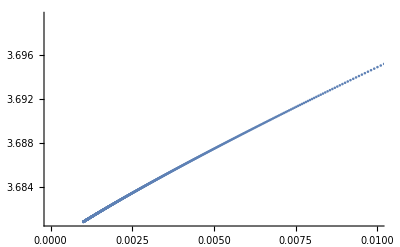

```mathematica
ListPlot[geomean,PlotRange->{{0.0,0.01},Automatic}]
```

```mathematica
geomean[[-1]]//N
Exp[Integrate[Log[x],{x,0,10}]/Integrate[1,{x,0,10}]]//N
```

{0.001,3.68083}

3.67879

```mathematica
list2=Table[With[{p=i},Table[i/(10p),{i,1,10*p}]],{i,1,100}];
geomean2=Table[{1/i,GeometricMean[list2[[i]]]},{i,1,100}];
geomean2//N
```

{{1.,0.452873},{0.5,0.415218},{0.333333,0.401483},{0.25,0.394213},{0.2,0.389665},{0.166667,0.386532},{0.142857,0.384232},{0.125,0.382467},{0.111111,0.381067},{0.1,0.379927},{0.0909091,0.378979},{0.0833333,0.378179},{0.0769231,0.377492},{0.0714286,0.376897},{0.0666667,0.376376},{0.0625,0.375915},{0.0588235,0.375504},{0.0555556,0.375136},{0.0526316,0.374804},{0.05,0.374502},{0.047619,0.374228},{0.0454545,0.373976},{0.0434783,0.373745},{0.0416667,0.373532},{0.04,0.373335},{0.0384615,0.373152},{0.037037,0.372981},{0.0357143,0.372822},{0.0344828,0.372673},{0.0333333,0.372533},{0.0322581,0.372402},{0.03125,0.372278},{0.030303,0.372161},{0.0294118,0.372051},{0.0285714,0.371946},{0.0277778,0.371847},{0.027027,0.371753},{0.0263158,0.371664},{0.025641,0.371579},{0.025,0.371498},{0.0243902,0.37142},{0.0238095,0.371346},{0.0232558,0.371275},{0.0227273,0.371207},{0.0222222,0.371142},{0.0217391,0.37108},{0.0212766,0.37102},{0.0208333,0.370963},{0.0204082,0.370907},{0.02,0.370854},{0.0196078,0.370803},{0.0192308,0.370753},{0.0188679,0.370705},{0.0185185,0.370659},{0.0181818,0.370615},{0.0178571,0.370572},{0.0175439,0.37053},{0.0172414,0.37049},{0.0169492,0.370451},{0.0166667,0.370413},{0.0163934,0.370376},{0.016129,0.370341},{0.015873,0.370306},{0.015625,0.370273},{0.0153846,0.37024},{0.0151515,0.370208},{0.0149254,0.370178},{0.0147059,0.370148},{0.0144928,0.370119},{0.0142857,0.37009},{0.0140845,0.370063},{0.0138889,0.370036},{0.0136986,0.37001},{0.0135135,0.369985},{0.0133333,0.36996},{0.0131579,0.369935},{0.012987,0.369912},{0.0128205,0.369889},{0.0126582,0.369866},{0.0125,0.369844},{0.0123457,0.369823},{0.0121951,0.369802},{0.0120482,0.369781},{0.0119048,0.369761},{0.0117647,0.369742},{0.0116279,0.369722},{0.0114943,0.369704},{0.0113636,0.369685},{0.011236,0.369667},{0.0111111,0.36965},{0.010989,0.369632},{0.0108696,0.369615},{0.0107527,0.369599},{0.0106383,0.369583},{0.0105263,0.369567},{0.0104167,0.369551},{0.0103093,0.369536},{0.0102041,0.369521},{0.010101,0.369506},{0.01,0.369492}}

```mathematica
Exp[Integrate[Log[x],{x,0,1}]/Integrate[1,{x,0,1}]]//N
```

0.367879

```mathematica
GMfinder[arg_,max_,min_]:=Exp[Integrate[arg[x],{x,min,max}]/Integrate[1,{x,min,max}]]//N
```

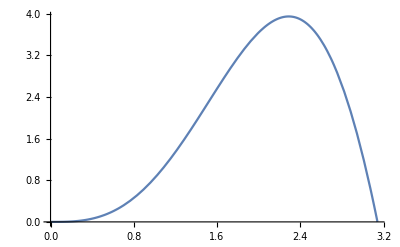

1.89008

```mathematica
Plot[x^2*Sin[x],{x,0,Pi}]
GMfinder[Sin,0,Pi]
```

```mathematica
Integrate[x*Sin[x],{x,0,Pi}]//N
Integrate[x*x^2*Sin[x],{x,0,Pi}]/Integrate[x^2*Sin[x],{x,0,Pi}]//N
Integrate[x^2*Sin[x],{x,0,Pi}]/Integrate[1,{x,0,Pi}]//N
```

3.14159

2.07113

1.86835

```mathematica
x^2*Sin[x]/.x->2.07113
```

3.76377

```mathematica
Expectation
```

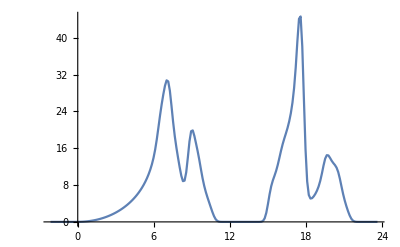

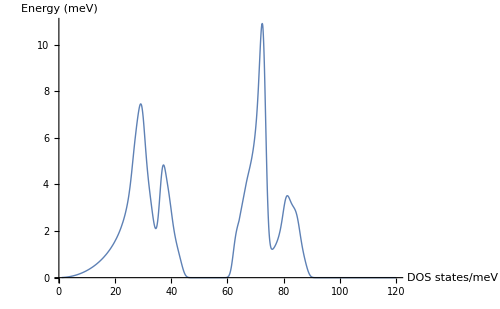

```mathematica
Import data;
THz2meV=1/4.135665538536;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/PERF_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllPERF=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
PERFdosFITs=Table[Interpolation[dosAllPERF[[i]]],{i,1,9}];
ListLinePlot@dosAllPERF[[1]]
Plot[Evaluate@Table[THz2meV*PERFdosFITs[[i]][x*THz2meV],{i,1,1}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
```

```mathematica
g[x_]:=Table[THz2meV*PERFdosFITs[[i]][x*THz2meV],{i,1,1}][[1]]
```

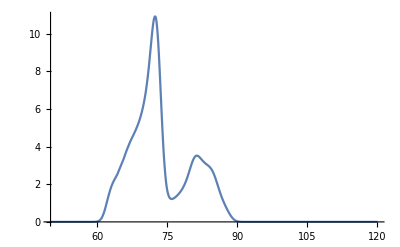

```mathematica
Plot[g[x],{x,50,120}]
```

```mathematica
upper=48
Integrate[g[x],{x,0,upper}]//N
(Integrate[x*g[x],{x,0,upper}]/Integrate[g[x],{x,0,upper}])//N
```

48

95.9995

29.6967

```mathematica
upper=50
Integrate[g[x],{x,0,upper}]//N
(Integrate[x*g[x],{x,0,upper}]/Integrate[g[x],{x,0,upper}])//N
```

50

95.9995

29.6967

```mathematica
GMfinder2[arg_,space_,max_,min_]:=Exp[Integrate[Log[arg]*space[x],{x,min,max}]/Integrate[space[x],{x,min,max}]]//N
AMfinder[arg_,space_,max_,min_]:=Integrate[arg*space[x],{x,min,max}]/Integrate[space[x],{x,min,max}]//N
```

```mathematica
GMfinder2[x,g,68,120]
AMfinder[x,g,68,120]
```

75.1722

75.3681

```mathematica
Exp[Integrate[Log[x]*g[x],{x,1,40}]/Integrate[g[x],{x,1,40}]]//N
```

27.8596